## Introduction

Rederive results in x here.

## Main

### Animation

```mathematica
SeedRandom[1];
{dt,T,n}={0.1,100,100};
{v0,k,σ}={1,1,3};
{R,L,Ω,d}={1,1,0.1,0};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{Z1,xs,ys,thetas}={{},{},{},{}};
While[t<NT,
znew=euler[z0,rhsVicsek,dt,v0,k,σ,ω,d];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,theta];
results=plotResultsVicsek[znew,L];
];
```

$Aborted

```mathematica
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
```

### No animation

## Correlation functions

### Methods

```mathematica
findVelAutoCorr[xs_,ys_,dt_,NT_]:=Block[{vx,vy,v,tcutoff,c},
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
tcutoff=Round[0.5*NT];
c=Table[
{tcutoff+t*dt,Sum[Normalize[v[[i,tcutoff]]].Normalize[v[[i,t]]],{i,1,n}]/n},
{t,tcutoff,NT-1}
];
Return[c]
]
```

```mathematica
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
```

```mathematica
v[[All,1]]//Length
```

50

### Make data

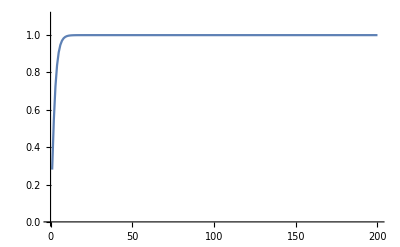

```mathematica
SeedRandom[1];
{dt,T,n}={0.25,50,50};
{v0,k,σ}={1,1,5};
{R,L,Ω,d}={1,1,0.1,0};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
{Zs,xs,ys,thetas}={{},{},{},{}};
While[t<NT,
znew=euler[z0,rhsVicsek,dt,v0,k,σ,ω,d];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,theta];AppendTo[Zs,findOrderPars[znew][[1]]];
];

ListPlot[Zs//Abs,Joined->True,PlotRange->{0,1.1}]
```

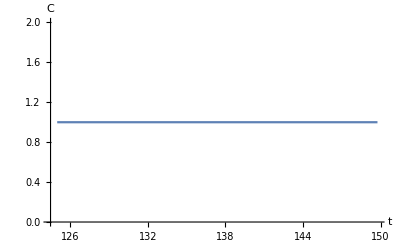

```mathematica
c=findVelAutoCorr[xs,ys,dt,NT];
ListPlot[c,AxesLabel->{"t","C"},LabelStyle->15,Joined->True,PlotRange->All]
```

### Multiple ensembles

```mathematica
run[d_]:=Block[{dt,T,n,v0,k,σ,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta},
{dt,T,n}={0.25,100,100};
{v0,k,σ}={1,1,2};
{R,L}={1,1};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
{Zs,xs,ys,thetas}={{},{},{},{}};
While[t<NT,
znew=euler[z0,rhsVicsek,dt,v0,k,σ,ω,d];
znew=(*periodizeMain[znew,1];*){x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,theta];
];

c=findVelAutoCorr[xs,ys,dt,NT];

Return[c]
]
```

#### Vary d

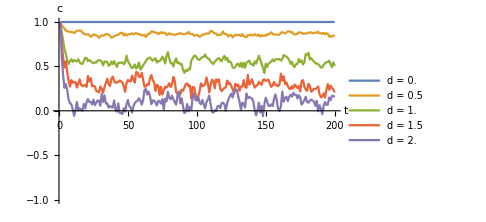

```mathematica
ds=Table[d,{d,0,2,0.5}];
cs=ParallelTable[run[d][[All,2]],{d,ds}];
p1=ListPlot[cs,Joined->True,PlotRange->{-1,1},ImageSize->Medium,AxesLabel->{"t","c"},LabelStyle->15,PlotLegends->Table["d = "<>ToString[ds[[i]]],{i,1,Length[ds]}]]
```

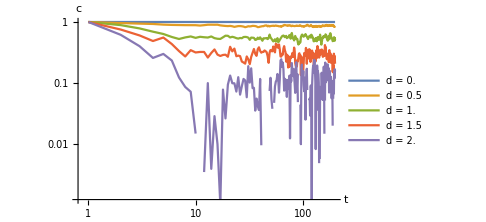

```mathematica
ListLogLogPlot[cs,Joined->True,PlotRange->{-1,1},ImageSize->Medium,AxesLabel->{"t","c"},LabelStyle->15,PlotLegends->Table["d = "<>ToString[ds[[i]]],{i,1,Length[ds]}]]
```

## Functions

```mathematica
heaviside[x_]:=Piecewise[{{1, x≥0}, {0, x<0}}];

rhsVicsek=Compile[{{z,_Real,2},{n,_Integer},{v0,_Real},{k,_Real},{σ,_Real},{ω,_Real,1}},
Module[{i,j,xji,yji,thetaji,dist,thetai,meanTheta,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
thetai=z[[3,i]];
meanTheta=0.0;
For[j=1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
dist=√(xji^2+yji^2);
meanTheta+= z[[3,j]]heaviside[σ-dist]/N[n];
];
vel[[1,i]]=v0 Cos[thetai];
vel[[2,i]]=v0 Sin[thetai];
vel[[3,i]]=k( meanTheta-thetai)
];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

rhs=Compile[{{z,_Real,2},{n,_Integer},{v0,_Real},{k,_Real},{σ,_Real},{ω,_Real,1}},
Module[{i,j,xji,yji,thetaji,dist,thetai,meanTheta,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
thetai=z[[3,i]];
meanTheta=0.0;
For[j=1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
dist=√(xji^2+yji^2);
meanTheta+= z[[3,j]]heaviside[σ-dist]/N[n];
];
vel[[1,i]]=v0 Cos[thetai];
vel[[2,i]]=v0 Sin[thetai];
vel[[3,i]]=k*(meanTheta-thetai)
];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];


findNoise[d_,n_,dt_]:=Block[{noise,zeros},
If[d>0,
zeros=Table[0.0,{i,1,n}];
noise={zeros,zeros,RandomVariate[NormalDistribution[0,√dt],n]},
noise=Table[0.0,{i,1,3},{j,1,n}]
];
Return[noise];
]

euler[z_,F_,dt_,v0_,k_,σ_,ω_,d_]:=Block[{znew,n,noise},
n=Dimensions[z][[2]];
noise=findNoise[d,n,dt];
Return[z+dt F[z,n,v0,k,σ,ω]+d*noise]
];

rk4[z_,F_,dt_,J_,K_,σ_,ω_,d_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,K,σ,ω,d];
k2=F[z+dt/2 k1,n,J,K,σ,ω,d];
k3=F[z+dt/2 k2,n,J,K,σ,ω,d];
k4=F[z+dt k3,n,J,K,σ,ω,d];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

plotResults[z_,L_]:=Block[{colors,p1,p2,p3,Z,Wp,Wm,meanX,meanY,ϕ,θ},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];

ϕ=ArcTan[z[[1,All]],z[[2,All]]];
θ=z[[3,All]];
p2=ListPlot[{ϕ//mod,θ//mod}ᵀ,AxesLabel->{"ϕ","θ"},LabelStyle->15,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium];

{Z,Wp,Wm}=findOrderPars[z];
{meanX,meanY}={Mean[z[[1,All]]],Mean[z[[2,All]]]};

p3=Graphics[{PointSize[0.06],
Cyan,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],
Magenta,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Pink,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Blue,Point[{meanX,meanY}],Black,Text["⟨x⟩",{meanX,meanY}],
Circle[{0,0},1]
},AxesOrigin->{0,0},PlotRange->{{-L,L},{-L,L}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,ImageSize->Medium];

Return[Grid[{{p1,p2,p3}}]];

];

findOrderPars[z_]:=Block[{Z,Wp,Wm,i,numOsc,ϕ,θ},
{Z,Wp,Wm}={0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
{ϕ,θ}={ArcTan[z[[1,i]],z[[2,i]]],z[[3,i]]};
Z+=Exp[ⅈ θ];
Wp+=Exp[ⅈ(ϕ+θ)];
Wm+=Exp[ⅈ(ϕ-θ)];;
];
Return[{Z/numOsc,Wp/numOsc,Wm/numOsc}]
];

findGamma[xs_,ys_]:=Block[{gamma,tolerance,phis,phi,s,temp,i,n},
n=Dimensions[xs][[2]];
gamma=0;
tolerance=0.05;
phis=ArcTan[xs,ys];
For[i=1,i≤n,i++,
phi=phis[[All,i]];
s=Sin[phi];
temp=(Max[s]-Min[s])/2;
If[temp>1-tolerance,gamma+=1];
];
Return[gamma/n]
];

findVelAutoCorr[xs_,ys_,n_,dt_]:=Block[{v,velAutoCorr},
velAutoCorr=Table[
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
{τ dt,Mean[Table[Normalize[v[[i,All,1]]].Normalize[v[[i,All,τ]]],{i,1,n}]]},
{τ,1,Length[xs]-1}
];
Return[velAutoCorr]
];

findV[xs_,ys_,dt_,n_]:=Block[{v},
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
Return[v]
];

findRijVijPairs[v_,xs_,ys_,t_,n_]:=Block[{dataRijVij,rij,vij,i,j},
dataRijVij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
vij=Normalize[v[[i,All,t]]].Normalize[v[[j,All,t]]];
AppendTo[dataRijVij,{rij,vij}]
]
];
dataRijVij=Sort[dataRijVij];
Return[dataRijVij]
];

findCr[xs_,ys_,dt_,n_,t_]:=Block[{v,dataRijVij,rs,vs,groupedRs,groupedVs,k,binr,binv,i,j,Cr},
v=findV[xs,ys,dt,n];
dataRijVij=findRijVijPairs[v,xs,ys,t,n];

(*Parition values*)
{rs,vs}={dataRijVij[[All,1]],dataRijVij[[All,2]]};
groupedRs=BinLists[rs,{0,3,0.05}];
groupedVs={};
k=1;
For[i=1,i≤Length[groupedRs],i++,
binr=groupedRs[[i]];
binv={};
For[j=1,j≤Length[binr],j++,
AppendTo[binv,vs[[k]]];
k+=1;
];
AppendTo[groupedVs,binv]
];

(*Find averages values*)
Cr=Table[
{Mean[groupedRs[[i]]],Mean[groupedVs[[i]]]},
{i,1,Length[groupedRs]}
];
Return[Cr]
];

findGr[xs_,ys_,n_,t_]:=Block[{i,j,rijs,rij,rs,gs,dr,rmax},
(* Find g(r) := radial density *)

(*Find pairwise rij*)
rijs={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
AppendTo[rijs,rij]
]
];

(*Radial density*)
{dr,rmax}={0.1,2};
rs=Table[i,{i,0.05,rmax,dr}];
gs=BinLists[rijs,{0,rmax,dr}];
gs=Table[Length[gs[[i]]]/(n(n-1))//N,{i,1,Length[gs]}];

Return[{rs,gs}]
];

periodize[z_,L_]:=Block[{znext},
Which[
z>L,Return[-L],
z<-L,Return[L],
True,Return[z]
]
];
SetAttributes[periodize,Listable];

periodizeMain[znew_,L_]:=Block[{x,y,theta},
{x,y,theta}=znew;
{x,y}={periodize[x,L],periodize[y,L]};
Return[{x,y,theta}]
];

plotResultsVicsek[z_,L_]:=Block[{x,y,θ,vx,vy,size,p1,p3,Z,Wp,Wm,L1},

(*Scatter plot*)
{x,y,θ}=z;
size=0.1;
{vx,vy}={Cos[θ],Sin[θ]};
p1=Graphics[{Arrowheads[Small],Table[Arrow[{{x[[i]],y[[i]]},{x[[i]]+size*vx[[i]],y[[i]]+size*vy[[i]]}}],{i,1,n}]},Axes->True,AxesLabel->{"x","y"},LabelStyle->15,PlotRange->{{-L,L},{-L,L}},ImageSize->Medium];

(*Order parameter*)
{Z,Wp,Wm}=findOrderPars[z];

L1=1.1;
p3=Graphics[{PointSize[0.06],
Cyan,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],Circle[{0,0},1]},AxesOrigin->{0,0},PlotRange->{{-L1,L1},{-L1,L1}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,ImageSize->Medium];

Return[Grid[{{p1,p3}}]];
];
```